# You can use a single program for everything: Mathematica 7

## Roman Shcherbakov, 30 Jan 2009, group meeting

## Manipulate: N-body simulation of a merger (single processor)

```mathematica
M1=5;
MinRad=5;
(* return the positions and velocities of the particles *)
posandvel[{a_,b_,c_},{r_,dr_},m_]:=
Module[{xp,yp,pos,unitvel,vel,xandy},
{xp,yp}=norms[{a,b,c}];
xandy=Select[Flatten[Table[{x,y},{x,-r,r,dr},{y,-r,r,dr}],1],(MinRad^2<(#.#)<r^2)&];
pos=Map[(xp #[[1]]+yp #[[2]])&,xandy];
unitvel=Map[((-#[[1]] yp+#[[2]] xp)/Sqrt[#[[1]]^2+#[[2]]^2])&,xandy];
vel=Map[#[[1]]*Sqrt[m/Sqrt[#[[2]].#[[2]]]]&,Transpose[{unitvel,pos}]];
{pos,vel}]
(* calculate the normal vectors to the velocities *)
norms[{x_,0|0.,0|0.}]:={{0,1,0},{0,0,1}}
norms[v_List]:=
Module[{w,u,wy,wz,ux,uy,uz},
w={0,wy,wz};
u={ux,uy,uz};
w=w/.First[NSolve[{w.v==0,w.w==1},{wy,wz}]];
u=u/.First[NSolve[{u.v==0,u.w==0,u.u==1},u]];
{w,u}]
CenterOfMass[{X1_,Y1_,Z1_},{X2_,Y2_,Z2_},{M1_,M2_}]:={(M1 X1+M2 X2)/(M1+M2),(M1 Y1+M2 Y2)/(M1+M2),(M1 Z1+M2 Z2)/(M1+M2)}
Initialize[Dist_,MF_,XX1_,XX2_,pos_,pos2_,vel_,vel2_,V1_,V2_,ss_,tcol_,icol_,vp_,TIME_,ir_,tr_,sep_]:=Module[{Rad1,Rad2,dr,intpl,Distlocal,MFlocal,M2local,poslocal,pos2local,vellocal,vel2local,XX1local,XX2local,V1local,V2local,sslocal,tcollocal,icollocal,vplocal,TIMElocal},
{Distlocal,Rad1,Rad2,dr,MFlocal,XX2local,V2local,intpl,sslocal,tcollocal,icollocal,vplocal,TIMElocal}={100,tr,ir,sep,MF,XX2,V2,Automatic,.001,Green,Cyan,{1.3,-2.4,2.},0};
intpl=V2local;
(*If[intpl===Automatic,intpl=V2local];*)
XX1local=V1local={0.,0.,0.};
M2local=MFlocal M1;
{poslocal,vellocal}=posandvel[{0,0,1},{Rad1,dr},M1];
{pos2local,vel2local}=posandvel[intpl,{Rad2,dr},M2local];
pos2local=Map[(#+XX2)&,pos2local];
vel2local=Map[(#+V2)&,vel2local];
{Distlocal,MFlocal,V1local,V2local,sslocal,tcollocal,icollocal,vplocal,TIMElocal,Sequence@@Realign[XX1local,XX2local,M2local,poslocal,pos2local],vellocal,vel2local}
]
Draw[XX1_,XX2_,MF_,pos_,pos2_,Dist_,TIME_,vp_,ss_,tcol_,icol_]:=Module[{cm=CenterOfMass[XX1,XX2,{M1,M1*MF}]},Graphics3D[{{tcol,PointSize[ss],Point[pos],PointSize[.025],Point[XX1]},{icol,PointSize[ss],Point[pos2],PointSize[.025],Point[XX2]}},BaseStyle->{GrayLevel[1]},AxesStyle->GrayLevel[.5],BoxStyle->GrayLevel[.5],PlotRange->{{-Dist+cm[[1]],Dist+cm[[1]]},{-Dist+cm[[2]],Dist+cm[[2]]},{-Dist+cm[[3]],Dist+cm[[3]]}},Axes->True,ViewPoint->vp,Background->GrayLevel[0],PlotLabel->"time = "<>ToString[TIME],ImageSize->{600,600},SphericalRegion->True,ImagePadding->20]]
(* update the center of mass *)
Realign[XX1_,XX2_,M2_,pos_,pos2_]:=
Module[{cm,poslocal,pos2local,XX1local,XX2local},
cm=CenterOfMass[XX1,XX2,{M1,M2}];
poslocal=Map[#-cm&,pos];
pos2local=Map[#-cm&,pos2];
XX1local=XX1-cm;
XX2local=XX2-cm;
{M2,poslocal,pos2local,XX1local,XX2local}]
(* iterate the simulation by one time step per call, assuming Keplerian orbits about the galaxy centers *)
Iterate[XX1_,XX2_,M2_,pos_,pos2_,vel_,vel2_,V1_,V2_,TIME_]:=Module[{a1,a2,acc,rr,ar1,ar2,poslocal,vellocal,pos2local,vel2local,XX1local,XX2local,V1local,V2local,TIMElocal},
(* starts in target galaxy *)
{poslocal,vellocal}=newstars[pos,vel,XX1,XX2,M1,M2];
(* starts in intruder galaxy *)
{pos2local,vel2local}=newstars[pos2,vel2,XX1,XX2,M1,M2];
(* two galaxies *)
rr=XX2-XX1;
ar1=M2*rr/(rr.rr)^(3/2);
ar2=-M1*rr/(rr.rr)^(3/2);
XX1local=XX1+V1+ar1/2;
XX2local=XX2+V2+ar2/2;
V1local=V1+ar1;
V2local=V2+ar2;
TIMElocal=TIME+1;
{poslocal,pos2local,vellocal,vel2local,XX1local,XX2local,V1local,V2local,TIMElocal}]
(* find the updated positions, velocities, and accelerations for all particles *)
newstars[pos_,vel_,XX1_,XX2_,M1_,M2_]:=
Module[{r1,r2,a1,a2,acc,newpos,newvel,delpos},
delpos=Position[pos,XX1|XX2];
newpos=Delete[pos,delpos];
newvel=Delete[vel,delpos];
r1=Map[(#-XX1)&,newpos];
r2=Map[(#-XX2)&,newpos];
a1=-Map[M1/Dot[#,#]^(3/2)*#&,r1];
a2=-Map[M2/Dot[#,#]^(3/2)*#&,r2];
acc=a1+a2;
newpos=newpos+newvel+acc/2;
newvel=newvel+acc;
{newpos,newvel}]


Manipulate[
If[t==0,
{Dist,MF,V1,V2,ss,tcol,icol,vp,TIME,M2,pos,pos2,XX1,XX2,vel,vel2}=Initialize[Dist,MF,XX1,{iposx,iposy,iposz},{iposx,iposy,iposz},pos2,vel,{ivelx,ively,ivelz},V1,{ivelx,ively,ivelz},ss,tcol,icol,vp,TIME,ir,tr,sep];
Draw[XX1,XX2,MF,pos,pos2,Dist,TIME,vp,.005,tcol,icol],Do[{pos,pos2,vel,vel2,XX1,XX2,V1,V2,TIME}=Iterate[XX1,XX2,M2,pos,pos2,vel,vel2,V1,V2,TIME],{step}];Draw[XX1,XX2,MF,pos,pos2,Dist,TIME,vp,.005,tcol,icol]],
{{tr,60,"target radius"},20,100,1,ControlPlacement->Top,Appearance->"Labeled"},
{{ir,20,"intruder radius"},20,100,1,ControlPlacement->Top,Appearance->"Labeled"},
{{sep,7,"star separation"},2,7,1,ControlPlacement->Top,Appearance->"Labeled"},
{{step,10,"step size"},1,10,ImageSize->Tiny,Appearance->"Labeled"},
{{MF,.1,"mass fraction"},.1,1,ImageSize->Tiny,Appearance->"Labeled"},
Delimiter,
Style["intruder initial position",Bold],
{{iposx,-50,"x"},-50,50,.01,ControlPlacement->Left,ImageSize->Tiny,Appearance->"Labeled"},
{{iposy,50,"y"},-50,50,.01,ControlPlacement->Left,ImageSize->Tiny,Appearance->"Labeled"},
{{iposz,50,"z"},-50,50,.01,ControlPlacement->Left,ImageSize->Tiny,Appearance->"Labeled"},
Delimiter,
Style["intruder initial velocity",Bold],
{{ivelx,0,"x"},-1,1,.01,ControlPlacement->Left,ImageSize->Tiny,Appearance->"Labeled"},
{{ively,-.33,"y"},-1,1,.01,ControlPlacement->Left,ImageSize->Tiny,Appearance->"Labeled"},
{{ivelz,-.33,"z"},-1,1,.01,ControlPlacement->Left,ImageSize->Tiny,Appearance->"Labeled"},
Delimiter,
{{reinit,False,""},Button["reinitialize",t=0]&},
{{t,0,"progress"},0,Infinity,ControlType->Trigger},
{{pos,{0,0,0}},ControlType->None},
{{vel,{0,0,0}},ControlType->None},
{{pos2,{-50,50,50}},ControlType->None},
{{vel2,{1,0,0}},ControlType->None},
{{XX1,{0,0,0}},ControlType->None},
{{XX2,{-50,50,50}},ControlType->None},
{{M2,.1},ControlType->None},
{{V1,{0,0,0}},ControlType->None},
{{V2,{1,0,0}},ControlType->None},
{{TIME,0},ControlType->None},
{{Dist,100},ControlType->None},
{{ss,.001},ControlType->None},
{{tcol,Green},ControlType->None},
{{icol,Cyan},ControlType->None},
{{vp,{1.3,-2.4,2.}},ControlType->None},AutorunSequencing->{1,2,3},TrackedSymbols:>{tr,ir,sep,step,reinit,t,MF,iposx,iposy,iposz,ivelx,ively,ivelz},SaveDefinitions->True,ControlPlacement->Left,ContentSize->{650,650}]
```

"Colliding Galaxies" from The Wolfram Demonstrations Project
http://demonstrations.wolfram.com/CollidingGalaxies/ 
Contributed by: Jeff Bryant and Dale Horton 
Based on a program by: Michael C. Schroeder and Neil F. Comins

## Manipulate: Saturn's Rings fly-by

```mathematica
Manipulate[Show[Graphics3D[{Specularity[GrayLevel[.3],1],RGBColor[.75,.7,.45],Sphere[{0,0,0},1],White,PointSize[.001],Point[stars]},Method->{"SpherePoints"->80}],(Graphics3D[{EdgeForm[GrayLevel[.3]],Lighter[RGBColor[.65,.6,.35],Rescale[(#[[1]]+#[[2]])/2,{1.24,2.30}]],Specularity[White,128],Ring[#[[1]],#[[2]]]}]&)/@Partition[Drop[Flatten[Nest[Flatten[({{#1⟦1⟧,#1⟦1⟧+1/3 (#1⟦2⟧-#1⟦1⟧)},{#1⟦2⟧-1/3 (#1⟦2⟧-#1⟦1⟧),#1⟦2⟧}}&)/@#1,1]&,{{1.24,2.30}},n]],1],2],ImageSize->{500,380},Background->Black,PlotRange->30,Lighting->{{"Ambient",GrayLevel[.2]},{"Directional",White,{0,-5,3}}},SphericalRegion->True,ViewVector->Dynamic[{{1.1,y,1},{1.5,0,0}},None],Boxed->False,ViewRange->{.9,30},ViewAngle->Pi/5],{{n,4,"number of iterations"},{0,1,2,3,4,5},ControlType->SetterBar},{{y,-10,"fly by"},-10,10},AutorunSequencing->{{1,4},{2,10}},Initialization:>{SeedRandom[12345];stars=20 Table[{Cos[#1]Sqrt[1-#2^2],Sin[#1]Sqrt[1-#2^2],#2}&[Random[Real,{0,2Pi}],Random[Real,{-1,1}]],{5000}];Ring[rMin_,rMax_]:=Polygon[Join[Table[rMin {Cos[a],Sin[a],0},{a,0,2 Pi,Pi/64}],Table[rMax {Cos[a],Sin[a],0},{a,0,2 Pi,Pi/64}]]]},ContentSize->{850,650}]
```

"Saturn's Rings and the Cantor Set" from The Wolfram Demonstrations Project
 http://demonstrations.wolfram.com/SaturnsRingsAndTheCantorSet/

Contributed by: Jeff Bryant

Suggested by: Stephen Wolfram

Based on a program by: Eric Rowland

## Manipulate: Diffusion-Limited Aggregation: A Real-Time Agent-Based Simulation (growth of dust particles)

```mathematica
initialAgents[n_]:=Developer`ToPackedArray[Append[
Table[Join[RandomReal[{0,1},2],{0.}],{n-1}],
{0.5,0.5,1.}]]
visualize[agents_]:=Module[{freeParticles=Select[agents,#[[3]]==0.&],fixedParticles=Select[agents,#[[3]]==1.&],dummyList={{-1,-1}}},
Show[
(* Plotting free particles *)
Graphics[{AbsolutePointSize[10],RGBColor[.33,.6,.7],
Point@If[freeParticles=={},dummyList,Map[Most,freeParticles]]}
],
(* Plotting fixed particles *)
Graphics[{AbsolutePointSize[10],RGBColor[.49,0,0],
Point@If[fixedParticles=={},dummyList,Map[Most,fixedParticles]]}
],
ImageSize->{350,350},
AspectRatio->Automatic,
Frame->False,
Axes->False,
PlotRange->{{0,1},{0,1}}
]
]
updateAgents[agents_,noise_]:=Module[
{nearestFixedParticles=Nearest[Most/@Select[agents,#[[3]]==1.&]],i,nextLocation,halfwayLocation},
Developer`ToPackedArray[
Table[
If[agents[[i,3]]==1.,
agents[[i]],(* If fixed, nothing changes *)
(* Otherwise, simulate random walk *)
nextLocation =Most[agents[[i]]]+RandomReal[{-noise,noise},2];
nextLocation=Clip[nextLocation,{0.,1.}];
halfwayLocation=(Most[agents[[i]]]+nextLocation)/2.;
If[
Norm[nearestFixedParticles[halfwayLocation][[1]]-halfwayLocation]<0.02,
Append[halfwayLocation,1.],
If[
Norm[nearestFixedParticles[nextLocation][[1]]-nextLocation]<0.02,
Append[nextLocation,1.],
Append[nextLocation,0.]
]
]
]
,{i,Length[agents]}
]
]
]
Manipulate[
Refresh[
If[sr≠oldsr,SeedRandom[sr];ag=initialAgents[n];oldsr=sr];
If[n≠oldn,SeedRandom[sr];ag=initialAgents[n];oldn=n];
If[moving,ag=updateAgents[ag,noiseLevel]];
visualize[ag]
,UpdateInterval->If[moving,0,Infinity]
]
,{{noiseLevel,0.01,"level of noise"},0,0.05,ImageSize->Tiny}
,{{n,100,"number of particles"},10,500,1,Appearance->"Labeled",ImageSize->Tiny}
,{{sr,123,"random seed"},1,12345,1,Appearance->"Labeled",ImageSize->Tiny}
,{{moving,False,"run simulation"},{True, False}}
,{{ag,SeedRandom[123];initialAgents[100]},ControlType->None}
,{{oldn,100},ControlType->None}
,{{oldsr,123},ControlType->None}
,SaveDefinitions->True,AutorunSequencing->{3},TrackedSymbols:>{noiseLevel,n,moving,ag,sr},SynchronousUpdating->True,ControlPlacement->Left
]
```

"Diffusion-Limited Aggregation: A Real-Time Agent-Based Simulation" from The Wolfram Demonstrations Project
 http://demonstrations.wolfram.com/DiffusionLimitedAggregationARealTimeAgentBasedSimulation/
Contributed by: Hiroki Sayama

## Plots: step by step

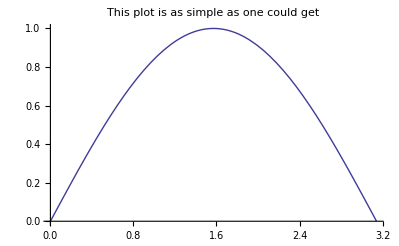

```mathematica
Plot[Sin[x],{x,0,π},PlotLabel->"This plot is as simple as one could get"]
```

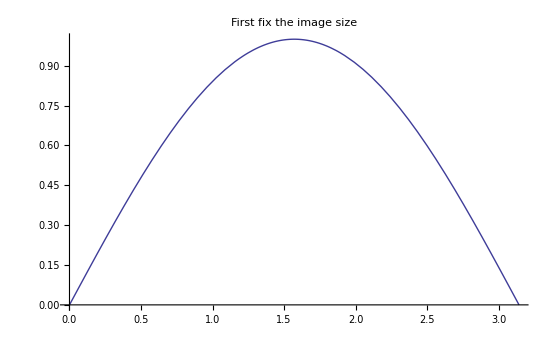

```mathematica
Plot[Sin[x],{x,0,π},ImageSize->550,PlotLabel->"First fix the image size"]
```

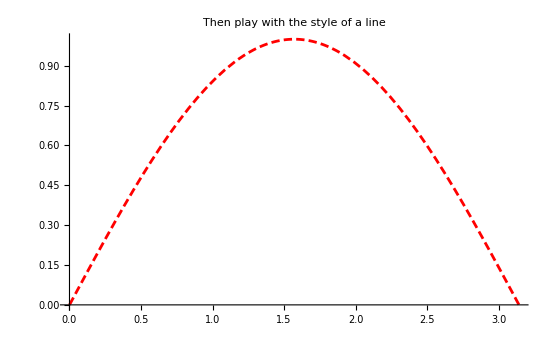

```mathematica
Plot[Sin[x],{x,0,π},ImageSize->550,PlotStyle->{Red,AbsoluteThickness[2],AbsoluteDashing[{6,3}]},PlotLabel->"Then play with the style of a line"]
```

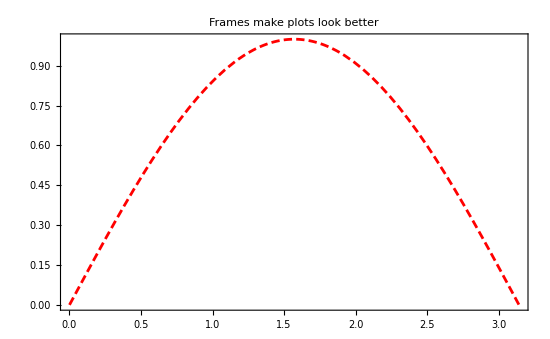

```mathematica
Plot[Sin[x],{x,0,π},ImageSize->550,Frame->True,FrameStyle->Directive[Blue,AbsoluteThickness[2]],PlotStyle->{Red,AbsoluteThickness[2],AbsoluteDashing[{6,3}]},PlotLabel->"Frames make plots look better"]
```

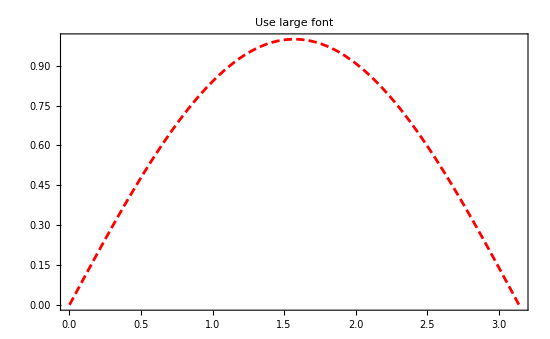

```mathematica
Plot[Sin[x],{x,0,π},ImageSize->550,Frame->True,FrameStyle->Directive[Blue,AbsoluteThickness[2]],PlotLabel->"Use large font",PlotStyle->{Red,AbsoluteThickness[2],AbsoluteDashing[{6,3}]},BaseStyle->{FontSize->16,FontFamily->"Arial",Bold}]
```

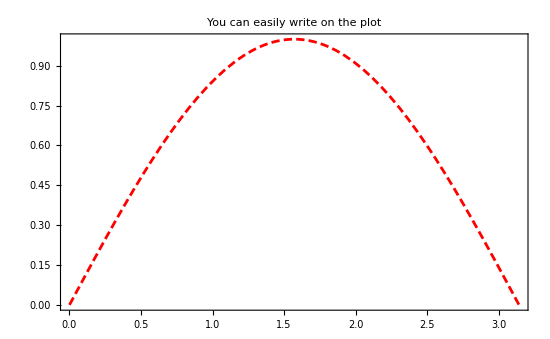

```mathematica
Plot[Sin[x],{x,0,π},ImageSize->550,Frame->True,FrameStyle->Directive[Blue,AbsoluteThickness[2]],PlotLabel->"You can easily write on the plot",PlotStyle->{Red,AbsoluteThickness[2],AbsoluteDashing[{6,3}]},BaseStyle->{FontSize->16,FontFamily->"Arial",Bold},Epilog->{Brown,Inset[Style["This is a nice plot",15,Bold],ImageScaled[{0.27,0.67}],{Center,Center},Automatic,{0.71,1}]}]
```

```mathematica
Plot[Sin[x],{x,0,π},ImageSize->550,Frame->True,FrameStyle->Directive[Blue,AbsoluteThickness[2]],PlotLabel->"Add some arrows",PlotStyle->{Red,AbsoluteThickness[2],AbsoluteDashing[{6,3}]},BaseStyle->{FontSize->16,FontFamily->"Arial",Bold},Epilog->{Brown,Inset[Style["This is a nice plot",15,Bold],ImageScaled[{0.6,0.57}],{Center,Center}],Black,AbsoluteThickness[3],Arrowheads[{0,0.03}],Arrow[{ImageScaled[{0.6,0.6}],ImageScaled[{0.72,0.72}]}]}]
```

-Graphics-

```mathematica
pll=
Plot[Sin[x],{x,0,π},ImageSize->550,Frame->True,FrameStyle->Directive[Blue,AbsoluteThickness[2]],PlotLabel->"Now add coordinate labels",FrameLabel->{{"y axis","Right label"},{"x axis","Top label"}},PlotStyle->{Red,AbsoluteThickness[2],AbsoluteDashing[{6,3}]},BaseStyle->{FontSize->16,FontFamily->"Arial",Bold},Epilog->{Brown,Inset[Style["Even better one",15,Bold],ImageScaled[{0.6,0.57}],{Center,Center}],Black,AbsoluteThickness[3],Arrowheads[{0,0.03}],Arrow[{ImageScaled[{0.6,0.6}],ImageScaled[{0.7,0.7}]}]}]
```

-Graphics-

```mathematica
pll=
Plot[{Sin[x],0.42x(π-x)},
{x,0,π},ImageSize->550,Frame->True,FrameStyle->Directive[Blue,AbsoluteThickness[2]],FrameLabel->{{"y axis",None},{"x axis","You can plot 2 or more functions together"}},PlotStyle->{{Red,AbsoluteThickness[2],AbsoluteDashing[{6,3}]},{Green,AbsoluteThickness[2],AbsoluteDashing[{1,0}]}},BaseStyle->{FontSize->16,FontFamily->"Arial",Bold},Epilog->{Brown,Inset[Style["Even better one",15,Bold],ImageScaled[{0.6,0.57}],{Center,Center}],Black,AbsoluteThickness[3],Arrowheads[{0,0.03}],Arrow[{ImageScaled[{0.6,0.6}],ImageScaled[{0.73,0.73}]}]}]
```

-Graphics-

```mathematica
pll=
Plot[{Sin[x],0.42x(π-x)},
{x,0,π},ImageSize->550,Frame->True,FrameStyle->Directive[Blue,AbsoluteThickness[2]],FrameLabel->{{"y axis",None},{"(1a)                                                                                  x axis","Now let us make a grid"}},PlotStyle->{{Red,AbsoluteThickness[2],AbsoluteDashing[{6,3}]},{Green,AbsoluteThickness[2],AbsoluteDashing[{1,0}]}},BaseStyle->{FontSize->16,FontFamily->"Arial",Bold},Epilog->{Brown,Inset[Style["Even better one",15,Bold],ImageScaled[{0.6,0.57}],{Center,Center}],Black,AbsoluteThickness[3],Arrowheads[{0,0.03}],Arrow[{ImageScaled[{0.6,0.6}],ImageScaled[{0.72,0.72}]}]}];
grr=GraphicsArray[{{pll,pll},{pll,pll}}]
```

-Graphics-

### Exporting image into EPS for a paper and viewing an image (*ask me if you want to resize a vector EPS graphics and have your fonts messed up while resizing*)

```mathematica
Export["C://study//accretion//! 2009 spring cfa//Group meetings//01-30//test.eps",pll](*Exporting file into EPS for a paper*)
Run["gsview32 \"C://study//accretion//! 2009 spring cfa//Group meetings//01-30//test.eps\""](*Viewing EPS file*)
```

C://study//accretion//! 2009 spring cfa//Group meetings//01-30//test.eps

0

## Plots: visualizing a scalar field

```mathematica
Clear[GRI,x,y,func,tt,ss];
acc=9;
step=0.15;csc=1;sc=4;
mm=(*step(√10000)/2*)0.15 79/2;A= mm/ArcCosh[200/mm];
points=Flatten[Outer[List,xtab=Table[i,{i,-mm,mm,step}],ytab=Table[i,{i,-mm,mm,step}]],1];
xy=(x=#[[1]];y=#[[2]];If[Abs[x]>Abs[y],{x,y}Cosh[Abs[x]/A],{x,y}Cosh[Abs[y]/A]])&/@points;
points={b->√((#[[1]])^2+(#[[2]])^2),β->ArcTan[10^-4+#[[1]],#[[2]]+10^-4]}&/@xy;Δ=0.001;
freqtab=Table[1.7 10^11 1.18^i,{i,-14,15}];


result04=Get["C:\\study\\mathematica\\! on desktop\\GRI04.dat"];
func[{x_,y_}]:=If[Abs[x]>Abs[y],{rxx=xx/.FindRoot[xx Cosh[xx/A]==x,{xx,1.}],y/x rxx},{ryy=yy/.(FindRoot[yy Cosh[yy/A]==y,{yy,1}]);x/y ryy,ryy}];
inGRI04=ListInterpolation[Log[10,Partition[10^-30+result04,Length[xtab]]],{xtab,ytab,Log[10,freqtab]},InterpolationOrder->4]

GRI04[x_?NumberQ,y_?NumberQ,ν_?NumberQ]:=Module[{tt,ss},10^({tt,ss}=If[Abs[x]>Abs[y],{rxx=xx/.FindRoot[xx Cosh[xx/A]==x,{xx,1.}],y/x rxx},{ryy=yy/.(FindRoot[yy Cosh[yy/A]==y,{yy,1}]);x/y ryy,ryy}];inGRI04[tt,ss,Log[10,ν]])];
```

InterpolatingFunction[{{-5.925,5.925},{-5.925,5.925},{10.2241,12.3087}},<>]

```mathematica
scale=GRI04[1,1,230 10^9];
ContourPlot[rr=Log[2,GRI04[x,y,230 10^9]/scale];If[rr<-0.5,0,rr],{x,-sc,sc},{y,-sc,sc},PlotPoints->30,Contours->30,ImageSize->600,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->16},PlotRange->All]
```

```mathematica
ttx=TimeUsed[];cpl230a04=DensityPlot[rr=Log[2,GRI04[x,y,230 10^9]/scale];If[rr<-0.5,0,rr],{x,-sc,sc},{y,-sc,sc},PlotPoints->100,ColorFunction->(RGBColor[2 #1 csc,#1csc,#1 csc]&),ImageSize->600,ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->16},PlotRange->All]
Print["Calculated in    ",  TimeUsed[]-ttx," seconds"]
```

Calculated in    12.421 seconds

```mathematica
ContourPlot[Log[2,GRI04[x,y,230 10^9]/scale],{x,-sc,sc},{y,-sc,sc},PlotPoints->30,Contours->30,ImageSize->600,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->16},PlotRange->All]
```

## Plots: visualizing a vector field

```mathematica
VectorPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3},ImageSize->600]
```

```mathematica
StreamPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3},ImageSize->600]
```

```mathematica
LineIntegralConvolutionPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3},ImageSize->600,RasterSize->300,LineIntegralConvolutionScale->0.6,ColorFunction->(GrayLevel[#]&),BaseStyle->{FontSize->16,FontFamily->"Arial",Bold},FrameStyle->AbsoluteThickness[2],PlotRange->All]
```

```mathematica
LineIntegralConvolutionPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3},ImageSize->600,RasterSize->300,LineIntegralConvolutionScale->0.6,ColorFunction->(GrayLevel[#]&),StreamPoints->Fine,StreamStyle->{"Line",Directive[Thin,LightGreen]},BaseStyle->{FontSize->16,FontFamily->"Arial",Bold},FrameStyle->AbsoluteThickness[2],PlotRange->All]
```

## Plots: the actual paper

```mathematica
Spherical accretion with MHD turbulence
```

## EventLocator: simple example with singularity (can be used to detect sonic points, horizon crossing)

NDSolve::ndsz: At t == 0.5, step size is effectively zero; singularity or stiff system suspected.

{x→InterpolatingFunction[{{0.,0.5}},<>]}

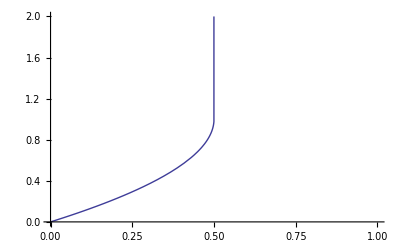

```mathematica
sol=NDSolve[{x'[t]==1/(1-x[t]),x[0]==0},x,{t,0,1}][[1]](*oops! singularity*)
Plot[x[t]/.sol,{t,0,1},PlotRange->{0,2}]
```

NDSolve::ndsz: At t == 0.5, step size is effectively zero; singularity or stiff system suspected.

{x→InterpolatingFunction[{{0.,0.5}},<>]}

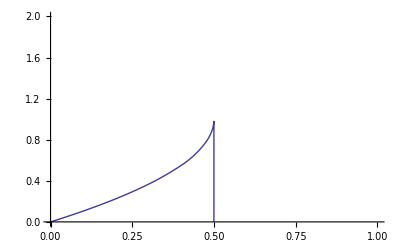

```mathematica
sol=NDSolve[{x'[t]==1/(1-x[t]),x[0]==0},x,{t,0,1},Method->"StiffnessSwitching"][[1]](*oops! singularity*)
Plot[x[t]/.sol,{t,0,1},PlotRange->{0,2}]
```

{x→InterpolatingFunction[{{0.,0.499999}},<>]}

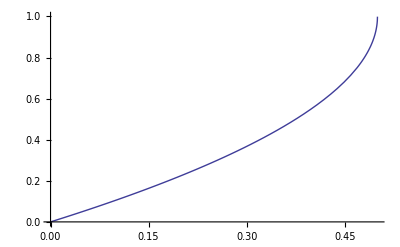

```mathematica
sol=NDSolve[{x'[t]==1/(1-x[t]),x[0]==0},x,{t,0,1},Method->{"EventLocator","Event"->x[t]-0.999,"EventAction":>{t11=t;Throw[Null, "StopIntegration"]}}][[1]](*oops! singularity*)
Plot[x[t]/.sol,{t,0,t11},PlotRange->{0,1}]
```

## EventLocator and Manipulate: geodesics in Schwarzschild metric

```mathematica
(*this part doesn't need to be modified*)Off[General::"unfl",General::"ovfl",InterpolatingFunction::"dmval"];
traj[dir_,bb_,r0_]:=(sw=1;ϕ1=20;d=dir;η:=If[sw==1&&Re[(1/b^2-1/r[ϕ]^2(1-1/r[ϕ]))]<10^-6.1,sw=-1;d=-d,d];
If[bb<0,ϕ1=-ϕ1;d=-d];
res=NDSolve[{r'[ϕ]==η r[ϕ]^2 √(1/b^2-1/r[ϕ]^2(1-1/r[ϕ])),r[0]==r0}/.b->bb,r,{ϕ,0,ϕ1}, StartingStepSize->10^-4,Method->{"EventLocator", "Event"->(Re[r[ϕ]]<10^-3)||(Re[r[ϕ]]>1000),"EventAction":> Throw[ϕ1 = ϕ, "StopIntegration"],"EventLocationMethod"->"LinearInterpolation",Method->"ExplicitRungeKutta"},MaxSteps->20000][[1]];
PolarPlot[r[ϕ]/.res,{ϕ,0,ϕ1},PlotRange->15,ImageSize->700,Frame->True,Epilog->Circle[]])
(√27.)/2
```

2.59808

```mathematica
Manipulate[traj[-1,impact,rad],Dynamic["Deflection angle "<>ToString[ ϕ1-π+ArcSin[impact/rad]]],Dynamic["Impact parameter  "<>ToString[impact]],Dynamic["Initial radius  "<>ToString[rad]],{{impact,15},1,15},{{rad,700},15,700}]
```

### Interactive equation solving (simple)

Enter text here. Enter an inline formula like this: 2+2.

```mathematica
Clear[x,t];num=1000;grid=2 Range[0,num]/num-1.;
sol=NDSolve[{D[u[x,t],t]+u[x,t]D[u[x,t],x]==0.004D[u[x,t],{x,2}],u[x,0]==Sin[π x],u[-1,t]==0,u[1,t]==0},u,{x,-1,1},{t,0,30},Method->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid", "Coordinates"->grid}}][[1]]
```

{u→InterpolatingFunction[{{-1.,1.},{0.,30.}},<>]}

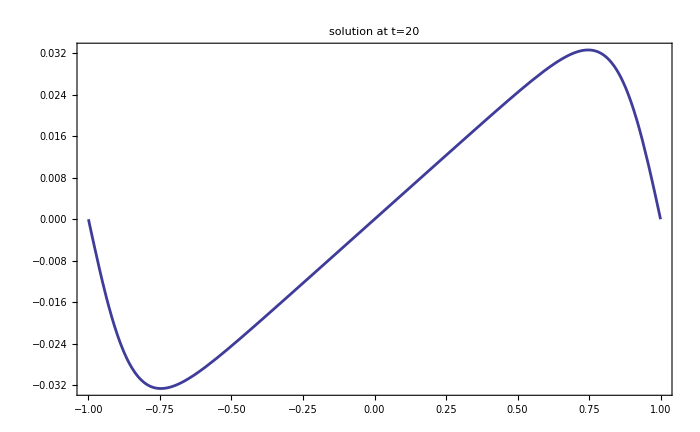

```mathematica
Plot[u[x,tt=20]/.sol,{x,-1,1},Frame->True,Axes->False,ImageSize->700,FrameStyle->AbsoluteThickness[2],PlotStyle->AbsoluteThickness[2],BaseStyle->{FontSize->15,FontFamily->"Times"},PlotLabel->"solution at  t="<>ToString[tt]]
```

## Eventlocator: probing the parameter dependence of the solution (non-linear oscillator)

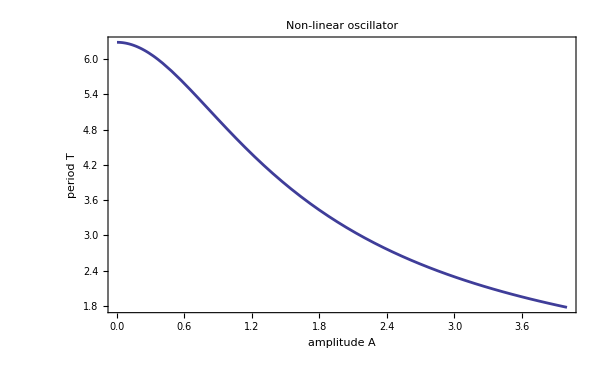

```mathematica
f[a_?NumberQ]:=(p=0;NDSolve[{x''[t]+x[t]+x[t]^3==0,x[0]==a,x'[0]==0},x,{t,∞},Method->{"EventLocator","Event"->x[t],"EventAction":>Throw[p=t,"StopIntegration"]}];
4p);
Plot[f[a],{a,0.001,4},Frame->True,FrameLabel->{"amplitude  A","period  T"},BaseStyle->{FontSize->16,FontFamily->"Times"},FrameStyle->AbsoluteThickness[2],PlotStyle->AbsoluteThickness[2],ImageSize->600,PlotLabel->"Non-linear oscillator"]
```

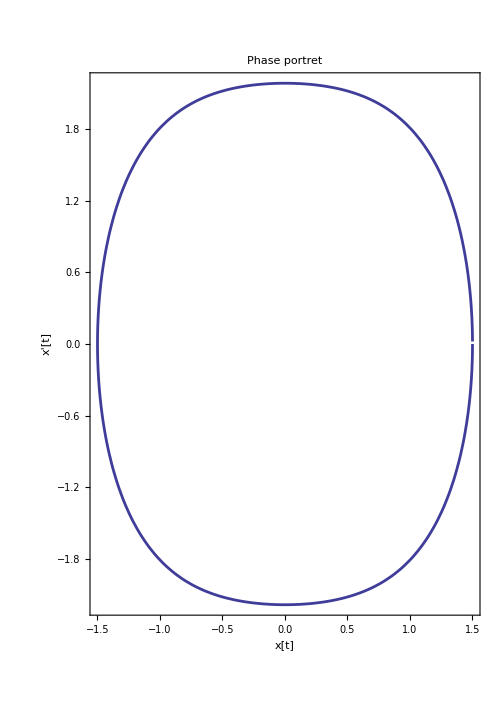

```mathematica
A=1.5;sol=First[NDSolve[{x''[t]+x[t]+x[t]^3==0,x[0]==A,x'[0]==0},x,{t,∞},Method->{"EventLocator","Event"->x[t]-0.99997A,Direction->1,"EventAction":>Throw[p=t,"StopIntegration"]}]];

ParametricPlot[{x[t]/.sol,x'[t]/.sol},{t,0,p},Frame->True,Axes->False,PlotLabel->"Phase  portret", FrameLabel->{"x[t]","x'[t]"},BaseStyle->{FontSize->16,FontFamily->"Times"},FrameStyle->AbsoluteThickness[2],PlotStyle->AbsoluteThickness[2],ImageSize->500]
```

## Interactive equation solving

```mathematica
ν = 0.075;num=40;xgrid=4. Range[-num,num]/num;ygrid=4. Range[-num,num]/num;
Off[NDSolve::"eerr",NDSolve::"eerri"];

Dynamic[Plot3D[u[i,x,y]/.sol3,{x,-4,4},{y,-4,4},PlotRange->{0,1},PlotLabel->"Solution at  t="<>ToString[i],ImageSize->700,BaseStyle->{FontSize->15,FontFamily->"Times"}]](*Dynamic updating of a plot*)

init=Exp[-(x^2+y^2)];
For[i=0,i≤2.9,i+=0.1,

sol3 = First[NDSolve[{D[u[t,x,y],t]==ν  (D[u[t,x,y],x,x]+D[u[t,x,y],y,y])-u[t,x,y] (2D[u[t,x,y],x]-  D[u[t,x,y],y]),u[i,x,y]==init,u[t,-4,y]==u[t,4,y], u[t,x,-4] == u[t,x,4]},u,{t,i,i+0.1},{x,-4,4},{y,-4,4}, Method->{"MethodOfLines", Method->{"FixedStep","StepSize"->0.009, Method->{"ExplicitRungeKutta","StiffnessTest"->False,"DifferenceOrder"->4}},"SpatialDiscretization"->{"TensorProductGrid",  "Coordinates"->{xgrid, ygrid}}}]];(*The actual iteration*)

init=ListInterpolation[Partition[(u[i+0.1,#[[1]],#[[2]]]/.sol3)&/@Flatten[Outer[List,xgrid,ygrid],1],Length[xgrid]],{xgrid,ygrid}][x,y](*Interpolation of the result of the previous step for the initial condition at the next step*)]
```

$Aborted

```mathematica
(*ν = 0.075;num=40;xgrid=4. Range[-num,num]/num;ygrid=4. Range[-num,num]/num;
Off[NDSolve::"eerr",NDSolve::"eerri"];

Dynamic[Plot3D[u[i-0.1,x,y]/.sol,{x,-4,4},{y,-4,4},PlotRange->{0,1},PlotLabel->"Solution at  t="<>ToString[i-0.1],ImageSize->700,BaseStyle->{FontSize->15,FontFamily->"Times"}]](*Dynamic updating of a plot*)

NDSolve`stop = False;
GUIRun[Widget["Panel", {Widget["Button",{
"label"->"Stop",
BindEvent["action",
Script[NDSolve`stop = True]]}]}]];


state=NDSolve`ProcessEquations[
{∂_t u[t,x,y]==ν  (∂_{x,2} u[t,x,y]+∂_{y,2} u[t,x,y])-u[t,x,y] (2∂_x u[t,x,y]-  ∂_y u[t,x,y]),u[0,x,y]==Exp[-(x^2+y^2)],u[t,-4,y]==u[t,4,y], u[t,x,-4] == u[t,x,4]},u,t,{x,-4,4},{y,-4,4}, Method->{"MethodOfLines", Method->{"FixedStep","StepSize"->0.009, Method->{"ExplicitRungeKutta","StiffnessTest"->False,"DifferenceOrder"->4}},"SpatialDiscretization"->{"TensorProductGrid",  "Coordinates"->{xgrid, ygrid}}}][[1]]

For[i=0.1,i≤3,i+=0.1,NDSolve`Iterate[state,i];sol = NDSolve`ProcessSolutions[state]]*)
```

NDSolve`StateData[<0.>]

```mathematica
ν = 0.075;num=40;xgrid=4. Range[-num,num]/num;ygrid=4. Range[-num,num]/num;
Off[NDSolve::"eerr",NDSolve::"eerri"];

Dynamic[Plot3D[u[i-0.1,x,y]/.sol,{x,-4,4},{y,-4,4},PlotRange->{0,1},PlotLabel->"Solution at  t="<>ToString[i-0.1],ImageSize->700,BaseStyle->{FontSize->15,FontFamily->"Times"}]](*Dynamic updating of a plot*)

(*NDSolve`stop = False;
GUIRun[Widget["Panel", {Widget["Button",{
"label"->"Stop",
BindEvent["action",
Script[NDSolve`stop = True]]}]}]];*)
NDSolve`stop=False;flag=False;caption="Click here to stop";
Button[Dynamic[caption],NDSolve`stop=True;flag=True;caption="Stopping. Wait..."]

state=NDSolve`ProcessEquations[
{D[u[t,x,y], t]==ν  (D[u[t,x,y], {x,2}]+D[u[t,x,y], {y,2}])-u[t,x,y] (2 D[u[t,x,y], x]-  D[u[t,x,y], y]),u[0,x,y]==Exp[-(x^2+y^2)],u[t,-4,y]==u[t,4,y], u[t,x,-4] == u[t,x,4]},u,t,{x,-4,4},{y,-4,4}, Method->{"MethodOfLines",Method->{"EventLocator","Event":>NDSolve`stop, Method->{"FixedStep","StepSize"->0.01, Method->{"ExplicitRungeKutta","StiffnessTest"->False,"DifferenceOrder"->4}}},"SpatialDiscretization"->{"TensorProductGrid",  "Coordinates"->{xgrid, ygrid}}}][[1]]

For[i=0.1,i≤100,i+=0.1,ii=i;If[flag,Break[]];NDSolve`Iterate[state,i];sol = NDSolve`ProcessSolutions[state]]
i=ii-0.1;caption="Stopped at i="<>ToString[i-0.1];
```

NDSolve`StateData[<0.>]

```mathematica
sol
```

{u→InterpolatingFunction[{{0.,0.45},{-4.,4.},{-4.,4.}},<>]}

## Inverting functions: chemical potential of Fermi gas as a function of temperature

```mathematica
Clear[μ,tt];Off[FindRoot::"lstol"];h=6.627*10^-27;k=1.38*10^-16;me=9.1*10^-28;mp=1.67*10^-24;
ρ=10^3;n=ρ/mp;
Ev=1.602*10^-12;
expr=n==Integrate[2/h^3 1/(Exp[(p^2/(2me)-10^3 Ev μ)/(10^3 Ev T)]+1)4π p^2,{p,0,+∞},GenerateConditions->False](*Implicit relation for temperature and chemical potential of Fermi gas*)
```

5.98802×10^26==-(1.90504×10^26 PolyLog[3/2,-ⅇ^((1. μ)/T)])/(1/T)^(3/2)

```mathematica
mu[tt_?NumberQ]:=(μ/.FindRoot[expr/.T->tt,{μ,0}]//Chop)(*Find chemical potential as a function of temperature*)
```

```mathematica
mu[2](*Calculate at some temperature*)
```

0.985052

```mathematica
LogLinearPlot[mu[T],{T,0.6,3.5},PlotStyle->{Blue,AbsoluteThickness[3]},Frame->True,FrameStyle->AbsoluteThickness[3],BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->18},FrameLabel->{"Temperature kT, keV","Chemical potential μ, keV"},ImageSize->550](*plot of mu[T] vs T*)
```

## Inverting functions: amplitude of a non-linear oscillator as a function of period

### Applicable to all boundary value problems

```mathematica
Clear[AA,a,amp,p];amp[p_?NumberQ]:=a/.(FindRoot[x[p]/.NDSolve[{x''[t]+x[t]+x[t]^3==0,x[0]==a,x'[0]==0},x,{t,p}],{a,1}]);
(*NDSolve inside FindRoot, syntax DOES matter*)

Off[NDSolve::"ndinnt",ReplaceAll::"reps"];(*The above evaluations produces error messages, but evaluates to the correct results, so switching the error messages off...*)

Plot[amp[p/4],{p,4,6.3},Frame->True,FrameLabel->{"period  T","amplitude  A"},BaseStyle->{FontSize->16,FontFamily->"Times"},FrameStyle->AbsoluteThickness[2],PlotStyle->AbsoluteThickness[2],ImageSize->600,PlotLabel->"Non-linear oscillator"]
```

## Parallelization, solving stiff equations: radiative transfer

```mathematica
Newtonian polarized and GR unpolarized radiative transfer
```

1. BDF Method for NDSolve is the best for stiff equations
2. ParallelTable can effectively be used for parallelization
3. There are memory leakages, so one needs to restart parallel kernels from time to time

## Working with the results of numerical simulations

```mathematica
Reading, averaging, writing, plotting the results of MHD simulation
```

1. BinaryReadList for fast reading from files (>20MB/s)
2. Only operations over the entire arrays, not elementwise (Total[], Average[], Array^2, Sin[Array])